John Lewis HW 4 904082686 mailto:johnlewis1928@gmail.com

Problem 1

```mathematica
Remove["Global`*"]

Manipulate[{ω0=2,a0=1,v0=0,
δβ=.1,lo=0,hi=10,βlo=0,βhi=4};
Plot[Evaluate[x[t]/.DSolve[{x''[t]+ 2 β x'[t] + ω0^2 x[t]==0 ,x[0]==a0,x'[0]==v0},x[t],t]],{t,lo,hi},PlotRange->{{lo,hi},{-1,1}}],{β,βlo,βhi},LocalizeVariables->True]
```

Problem 2

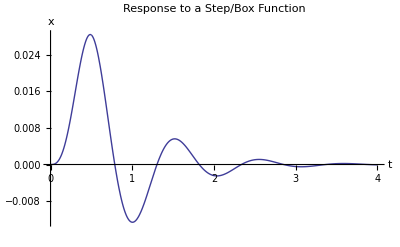

```mathematica
Remove["Global`*"]
ℱ[t_]=m Piecewise[{{a Sin[ω t],0<t<Pi/ω}},0];
osc=x''[t]+2 β x'[t] + ω^2 x[t];
β=Pi/2;ω=2 Pi;a=1;
tlo=0;thi=8 Pi/ω;
tmid=Pi/ω;
x1[t_]=x[t]/.DSolve[{osc==0,x[tlo]==0,x'[tlo]==0},x[t],t][[1]];
x2[t_]=x[t]/.DSolve[{osc==a Sin[ω t],x[tlo]==x1[tlo],x'[tlo]==x1'[tlo]},x[t],t][[1]];
x3[t_]=x[t]/.DSolve[{osc==0,x[tmid]==x2[tmid],x'[tmid]==x2'[tmid]},x[t],t][[1]];
plot:=Plot[x1[t],{t,-4,0}]
plot1:=Plot[Evaluate[x2[t]],{t,0,Pi/ω},PlotRange->All]
plot3:=Plot[Evaluate[x3[t]],{t,Pi/ω,thi},PlotRange->All]
Show[{plot1,plot3},PlotRange->All,PlotLabel->"Response to a Step/Box Function",AxesLabel->{"t","x"}]
```

Problem 3

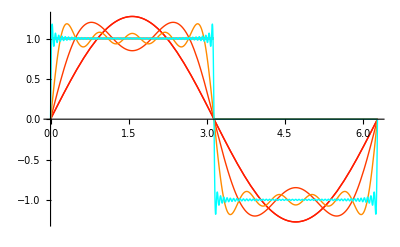

```mathematica
Remove["Global`*"]

f[x_]=Piecewise[{{1,0<x<Pi}},0];
c[n_]=FourierCosCoefficient[f[x],x,n];
s[n_]=FourierSinCoefficient[f[x],x,n];
a[n_]=2/Pi Integrate[f[x]*Cos[n x],{x,0,Pi}];
b[n_]=2/Pi Integrate[f[x]*Sin[n x],{x,0,Pi}];
Table[element[i]={c[i], a[i]+a},{i,1,5}]//MatrixForm;
Table[element[i]={s[i],b[i]},{i,1,5}] //MatrixForm;
p[u_]:=Plot[{Sum[a[m] Cos[m x]+b[m] Sin[m x],{m,1,u}],f[x]},{x,0,2 Pi},PlotStyle->Hue[u/(u+100)]]
Show[p[1],p[2],p[4],p[10],p[100]]
```

Problem 4

{{0,2/π},{1,0},{2,-2/(3 π)},{3,0},{4,-2/(15 π)},{5,0},{6,-2/(35 π)},{7,0},{8,-2/(63 π)},{9,0},{10,-2/(99 π)},{11,0},{12,-2/(143 π)},{13,0},{14,-2/(195 π)},{15,0},{16,-2/(255 π)},{17,0},{18,-2/(323 π)},{19,0},{20,-2/(399 π)}}

{{0,0},{1,1/2},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0}}

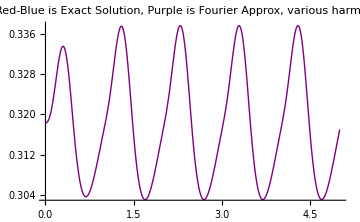

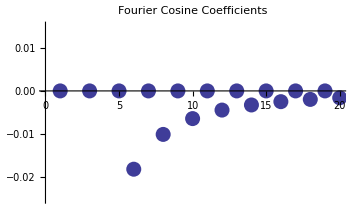

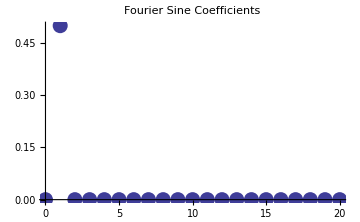

```mathematica
Remove["Global`*"]
T=2 π/ω;nhi=20;
F[t_]=Sin[ω t](*Piecewise[{{ Sin[ω t],0<t<(Pi/ω)},{0,Pi/ω<t<2 Pi/ω}},0]*) ;
a[n_]:= (2/T) Integrate[F[t]*Cos[n ω t],{t,0,π/ω},Assumptions->{ω ϵ Reals,ω>0}];
b[n_]:=(2/T) Integrate[F[t]*Sin[n ω t],{t,0,π/ω},Assumptions->{ω ϵ Reals,ω>0}];
(*f[b_,t_]:=a[0]/2 +Sum[a[n] Cos[n ω t]+b[n] Sin[n ω t],{n,1,b}]*)
alist=Table[{n,a[n]},{n,0,nhi}]
blist=Table[{n,b[n]},{n,0,nhi}]
(******************************************)
osc[t_]=x''[t]+2 β x'[t] + ω0^2 x[t];
xcos[n_,t_]=x[t]/.DSolve[{osc[t]==Cos[n ω t],x[0]==0,x'[0]==0},x[t],t][[1]];
xsin[n_,t_]=x[t]/.DSolve[{osc[t]==Sin[n ω t],x[0]==0,x'[0]==0},x[t],t][[1]] ;
x1[t_]=x[t]/.DSolve[{osc[t]==Sin[ω t],x[0]==0,x'[0]==0},x[t],t][[1]];
x2[t_]=x[t]/.DSolve[{osc[t]==0,x[Pi/ω]==x1[π/ω],x'[Pi/ω]==x1'[Pi/ω]},x[t],t];
(*********************************************)
β=ω/2;ω=2 Pi;ω0=ω;tlo=0;thi=5 T;
p1:=Plot[x1[t],{t,0,thi},PlotRange->All,PlotStyle->{Red}]
p2:=Plot[x2[t],{t,Pi/ω,thi},PlotRange->All,PlotStyle->{Blue}];
P[b_]:=Plot[alist[[1,2]]/2+Sum[alist[[n,2]] xcos[n,t]+blist[[n,2]] xsin[n,t],{n,1,b}],{t,tlo,thi},PlotStyle->{Purple},PlotRange->All];
Nh[c_]:=Plot[xcos[0,t]/2+xcos[c,t]+xsin[c,t],{t,tlo,thi},PlotStyle->Hue[c/(c+10)]];
plota:=ListPlot[alist,PlotStyle->PointSize[.03],PlotLabel->"Fourier Cosine Coefficients"]
plotb:=ListPlot[blist,PlotStyle->PointSize[.03],PlotLabel->"Fourier Sine Coefficients"]
Show[P[nhi],PlotLabel->"Red-Blue is Exact Solution, Purple is Fourier Approx, various harmonics",ImageSize->Medium]
plota
plotb
```

Problem 5

Piecewise[{{0., t≤0}, {ⅇ^(-1. t) (0.450708 Cos[t]+ⅇ^(0.7 t) (-0.450708 Cos[0.953939 t]+0.195738 Sin[0.953939 t])+0.128774 Sin[t]), True}}]

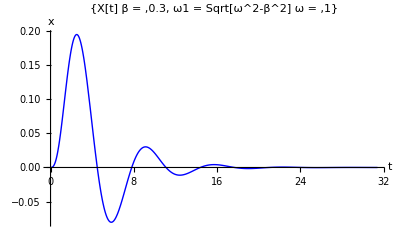

```mathematica
Remove["Global`*"]
γ=1;F0=3;
ω=1;ω1=Sqrt[ω^2-β^2];
m=4;β=.3;
tlo=0;thi=10 Pi;
F[t1_]=Piecewise[{{F0 ⅇ^(-γ t1) Sin[t1 ω],t1>0},{0,t1<0}},0];
G[t_,t1_]=Piecewise[{{(ω1 ⅇ^(-β (t-t1)) Sin[ω1 (t-t1)])/m,t≥t1},{0,t<t1}},0];
x=Integrate[F[t1] G[t,t1],{t1,-∞,t},Assumptions->t∈Reals] //FullSimplify //TrigToExp
f=Integrate[F[t1],{t1,-∞,t},Assumptions->t∈Reals];
g=Integrate[G[t,t1],{t1,-∞,t},Assumptions->t∈Reals];
Plot[{x},{t,tlo,thi},PlotStyle->{Red,Green,Blue},PlotRange->All,AxesLabel->{"t","x"},PlotLabel->{"X[t]  β = ",β," ω1 = Sqrt[ω^2-β^2]   ω = ",ω}]
```

Problem 6

```mathematica
Remove["Global`*"]
f=-A r[t]^(α-1);
U=Integrate[f,r[t]]+m g Sin[θ[t]];
T=1/2 m (v[t].v[t]);
L=T-U;
clist={m,g,α};
v[t_]={r'[t],r[t] θ'[t]};
ELr=D[L,r[t]]-Dt[D[L,r'[t]],t,Constants->clist];
ELθ=D[L,θ[t]]-Dt[D[L,θ'[t]],t,Constants->clist];
Print["Lagrange for r: ",ELr//TraditionalForm];
Print["Lagrange for θ: ",ELθ//TraditionalForm];
Print["Is angular momentum conserved?"]
Print["No"]
```

Lagrange for r: A (r(t))^(α-1)-m r''(t)+m r(t) (θ'(t))^2

Lagrange for θ: -g m cos(θ(t))-2 m r(t) r'(t) θ'(t)-m (r(t))^2 θ''(t)

Is angular momentum conserved?

No